Transport in a Rabi triangle with photon hopping
To have more cavities, change the variable “nlat”
Interplay between multiphoton resonance and photon hopping

Module 1: Basic setting
Basis arrangement: (|e,0; e,0; e,0> |e,0; e,0; g,0> |e,0; e,0; e,1> |e0; e,0; g,1> ... )
The basis changes from the last cavity to the first cavity. 
Hopping operator can be right-ordered in Kronecker product command

```mathematica
Timing[
Clear["Global`*"];
kron=Fold[KroneckerProduct]; (* Nested Kronecker product *)

nphoton=5; (* Max photon number *)
dim=2*(nphoton+1); (* Dimension of Hilbert space for one cavity *)
np=3;(* multiphoton resonance *)
max=500;(* eigenvectors wanted *)

λ=0.02; (* One-photon strength *)
κ=0; (* Two-photon strength *)
ωcr=1/np+2np(np+1)/(np^2-1)*λ^2+2np(np^2+np-2)/(np^2-4)*κ^2;

nlat=3;(* Total number of lattice sites *)

σz={{1,0},{0,-1}}; (* Pauli z for atom *)
σx={{0,1},{1,0}}; (* Pauli x for atom *)
σp={{0,1},{0,0}}; (* Raising for atom *)
σm={{0,0},{1,0}}; (* Lowering for atom *)

idenphoton=SparseArray[{i_,i_}->1.,{nphoton+1,nphoton+1}];
idenatom=IdentityMatrix[2];
iden=SparseArray[{i_,i_}->1.,{dim,dim}];
idenbigbig=SparseArray[{i_,i_}->1.,{dim^nlat,dim^nlat}];

(* Annihilation for photon *)
a=SparseArray[{{i_,j_}/;j-i==1->N[Sqrt[i]]},{nphoton+1,nphoton+1}];

(* Creation for photon *)
adag=Transpose[a];

(* Rabi Hamiltonian for single cavity *)
  Hs[ωa_,ωc_]:=ωa/2*KroneckerProduct[idenphoton,σz]+ωc*KroneckerProduct[adag.a,idenatom]+λ*KroneckerProduct[a+adag,σx]+κ*KroneckerProduct[a.a+adag.adag,σx]; 

(* JC-Hamiltonian *)
(*  Hs[ωa_,ωc_]:=ωa/2*KroneckerProduct[idenphoton,σz]+ωc*KroneckerProduct[adag.a,idenatom]+λ*KroneckerProduct[a,σp]+λ*KroneckerProduct[adag,σm]+κ*KroneckerProduct[a.a,σp]+κ*KroneckerProduct[adag.adag,σm]; *)

(* Frequency profile for each cavity *)
ωa={1,1,1,1,1}; 
ωc={ωcr,ωcr,ωcr,ωcr,ωcr}; 
Print["Resonant frequency: ",ωcr];

(* Hamiltonian without hopping *)
H0=Sum[kron[Join[Table[iden,i-1],{Hs[ωa[[i]],ωc[[i]]]},Table[iden,nlat-i]]],{i,1,nlat}];
Print["Byte Count for H0: ",ByteCount[H0]]

(* pos=Sum[(2n[[i]]+1-α[[i]])*dim^(nlat-i),{i,1,nlat}]+1; *)
]
```

Resonant frequency: 0.334533

Byte Count for H0: 291568

{0.028326,Null}

Module 2 : Hopping matrix
Hopping operator: a_n^†a_m, must be n>m
Comment: Transfer photon from the m-th to the n-th cavity

```mathematica
Timing[
(* Ω=λ; *)
  (* Ω=9Sqrt[6]λ^3/4+27Sqrt[6]λ*κ^2; *)
  Ω=(128Sqrt[6]/9)*λ^2*κ ; 

η=1/4;
J=η*(4/(nlat*Sqrt[nlat]))*Ω;

θ=π/6;

nnonzero=4*nphoton^2*(2(nphoton+1))^(nlat-2); (* No of non-zero elements for hopping terms *)
Print["No of non-zero terms: ",nnonzero];
Clear[nnonzero];

num[n_]:=kron[Join[Table[iden,n-1],{adag.a},{idenatom},Table[iden,nlat-n]]];
spin[n_]:=kron[Join[Table[iden,n-1],{idenphoton},{σp.σm},Table[iden,nlat-n]]];
hop[m_,n_]:=kron[Join[Table[iden,m-1],{a},{idenatom},Table[iden,n-m-1],{adag},{idenatom},Table[iden,nlat-n]]];

V[θ_]:=Sum[hop[i,i+1]*Exp[-ⅈ*θ],{i,1,nlat-1}]+Transpose[hop[1,nlat]]*Exp[-ⅈ*θ];

H=H0+J*V[θ]+J*ConjugateTranspose[V[θ]];
Print["Byte count for H :",ByteCount[H]]
]
```

No of non-zero terms: 4608

Byte count for H :1553264

{0.027172,Null}

Module 3 : Time evolution and calculate the observables from dot product
Dynamics is obtained by solving the Hamiltonian, and use linear superposition of eigenstates 
Caution: Check the norm of the final vector for safety

```mathematica
TR=π/Ω//N;
TH=2π/(Sqrt[nlat]*J)//N; 
(* tf=5*Min[TR,TH]; *)
tf=15TH;

tN=800;

(* Initial state *)
n={0,0,0,0,0};
α={1,0,0,0,0};
pos=Sum[(2n[[i]]+1-α[[i]])*dim^(nlat-i),{i,1,nlat}]+1;

initial=Table[0.,{k,1,dim^nlat}];
initial[[pos]]=1.;

Timing[
ff=100-Eigenvalues[100*idenbigbig-H,max];
gg=Eigenvectors[100*idenbigbig-H,max]//Chop;
Ψ[t_]:=Sum[(initial.Conjugate[gg[[i]]])*Exp[-ⅈ*ff[[i]]*t]*gg[[i]],{i,1,max}];
Print["norm after projection: ",Norm[Ψ[0]]];
]

Do[list[i]={};,{i,1,nlat}];
Do[spinlist[i]={};,{i,1,nlat}];

Timing[
Do[
wavfn=Ψ[t]//Chop;
Do[list[i]=Append[list[i],{t/TH,Conjugate[wavfn].num[i].wavfn//Chop}];,{i,1,nlat}];
Do[spinlist[i]=Append[spinlist[i],{t/TH,Conjugate[wavfn].spin[i].wavfn//Chop}];,{i,1,nlat}];

,{t,0,tf,tf/tN}]; 
]
```

Eigenvalues::arh: Because finding 500 out of the 1728 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

Eigenvectors::arh: Because finding 500 out of the 1728 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvectors.

norm after projection: 1.

{10.2308,Null}

{692.061,Null}

Case 1: 3-ph resonance, λ=0.02, κ=0. 
Plot the observables (μ=1/5, θ=π/6)

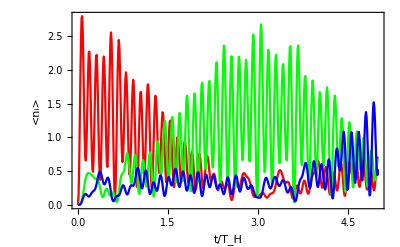

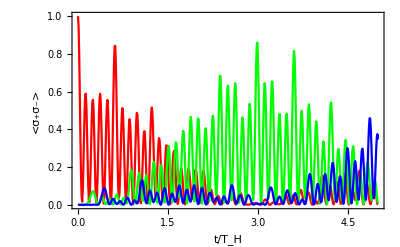

```mathematica
ListPlot[{list[1],list[2],list[3]},PlotStyle->{Red,Green,Blue,Purple,Pink},PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t/T_H","<n_i>"}]
ListPlot[{spinlist[1],spinlist[2],spinlist[3]},PlotStyle->{Red,Green,Blue,Purple,Pink},PlotRange->All,Joined->True,AxesOrigin->{0,0},Frame->True,FrameLabel->{"t/T_H","<σ_+σ_->"}]
```

Case 2: 4-ph resonance, λ=0.05, κ=0.01. 
Plot the observables (μ=1/2, θ=π/6)

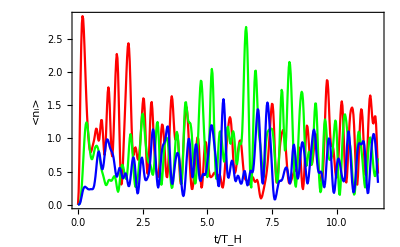

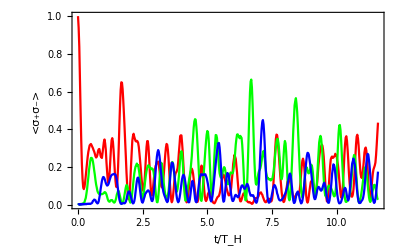

```mathematica
ListPlot[{list[1],list[2],list[3]},PlotStyle->{Red,Green,Blue,Purple,Pink},PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t/T_H","<n_i>"}]
ListPlot[{spinlist[1],spinlist[2],spinlist[3]},PlotStyle->{Red,Green,Blue,Purple,Pink},PlotRange->All,Joined->True,AxesOrigin->{0,0},Frame->True,FrameLabel->{"t/T_H","<σ_+σ_->"}]
```

Case 3: 4-ph resonance, λ=0.05, κ=0.01. 
Plot the observables (μ=1/10, θ=π/6)

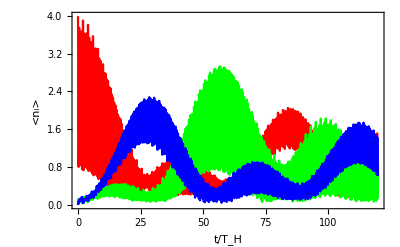

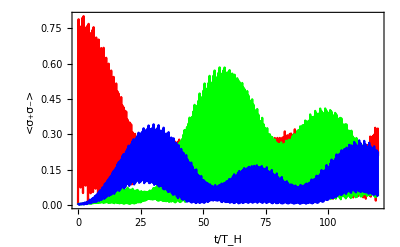

```mathematica
ListPlot[{list[1],list[2],list[3]},PlotStyle->{Red,Green,Blue},PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t/T_H","<n_i>"}]
ListPlot[{spinlist[1],spinlist[2],spinlist[3]},PlotStyle->{Red,Green,Blue},PlotRange->All,Joined->True,AxesOrigin->{0,0},Frame->True,FrameLabel->{"t/T_H","<σ_+σ_->"}]
```

Case 4a: 3-ph resonance, λ=0.02, κ=0. NO RWA
Plot the observables (μ=1/4, θ=π/6)

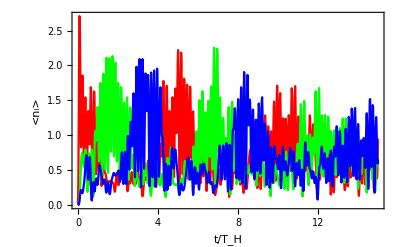

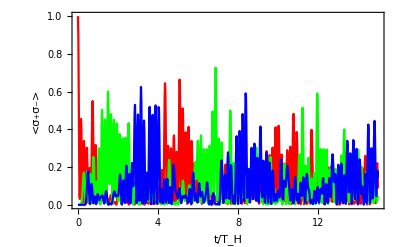

```mathematica
ListPlot[{list[1],list[2],list[3]},PlotStyle->{Red,Green,Blue,Purple,Pink},PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t/T_H","<n_i>"}]
ListPlot[{spinlist[1],spinlist[2],spinlist[3]},PlotStyle->{Red,Green,Blue,Purple,Pink},PlotRange->All,Joined->True,AxesOrigin->{0,0},Frame->True,FrameLabel->{"t/T_H","<σ_+σ_->"}]
```

Case 4b: 3-ph resonance, λ=0.02, κ=0. WITH RWA
Plot the observables (μ=1/4, θ=π/6)

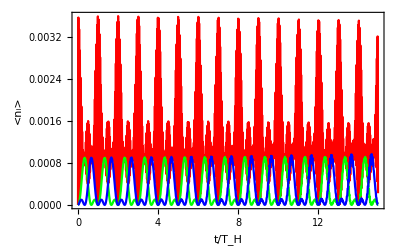

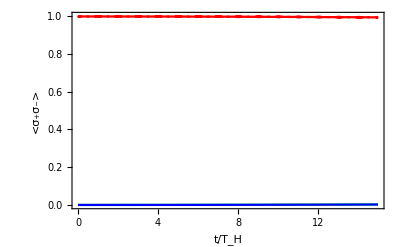

```mathematica
ListPlot[{list[1],list[2],list[3]},PlotStyle->{Red,Green,Blue,Purple,Pink},PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t/T_H","<n_i>"}]
ListPlot[{spinlist[1],spinlist[2],spinlist[3]},PlotStyle->{Red,Green,Blue,Purple,Pink},PlotRange->All,Joined->True,AxesOrigin->{0,0},Frame->True,FrameLabel->{"t/T_H","<σ_+σ_->"}]
```